## Calculations for the study about resilience of gene regulation

See Quad P2.4, 27/2/25 for sketches and calculations

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False]
```

#### Get equilibria of the n=2 system (exact)

```mathematica
Solve[a*(x^2)/(1+x^2)-x+r==0,x]
```

{{x→(a+r)/3+(2^(1/3) (3-(a+r)^2))/(3 (9 a-2 a^3-18 r-6 a^2 r-6 a r^2-2 r^3+3 √3 √(4-a^2-20 a r+4 a^3 r+8 r^2+12 a^2 r^2+12 a r^3+4 r^4))^(1/3))-((9 a-2 a^3-18 r-6 a^2 r-6 a r^2-2 r^3+3 √3 √(4-a^2-20 a r+4 a^3 r+8 r^2+12 a^2 r^2+12 a r^3+4 r^4))^(1/3))/(3 2^(1/3))},{x→(a+r)/3-((1+ⅈ √3) (3-(a+r)^2))/(3 2^(2/3) (9 a-2 a^3-18 r-6 a^2 r-6 a r^2-2 r^3+3 √3 √(4-a^2-20 a r+4 a^3 r+8 r^2+12 a^2 r^2+12 a r^3+4 r^4))^(1/3))+((1-ⅈ √3) (9 a-2 a^3-18 r-6 a^2 r-6 a r^2-2 r^3+3 √3 √(4-a^2-20 a r+4 a^3 r+8 r^2+12 a^2 r^2+12 a r^3+4 r^4))^(1/3))/(6 2^(1/3))},{x→(a+r)/3-((1-ⅈ √3) (3-(a+r)^2))/(3 2^(2/3) (9 a-2 a^3-18 r-6 a^2 r-6 a r^2-2 r^3+3 √3 √(4-a^2-20 a r+4 a^3 r+8 r^2+12 a^2 r^2+12 a r^3+4 r^4))^(1/3))+((1+ⅈ √3) (9 a-2 a^3-18 r-6 a^2 r-6 a r^2-2 r^3+3 √3 √(4-a^2-20 a r+4 a^3 r+8 r^2+12 a^2 r^2+12 a r^3+4 r^4))^(1/3))/(6 2^(1/3))}}

#### First derivative of the n=n system, and critical parameter

```mathematica
D[a*(x^n)/(1+x^n)-x+r,x]
```

-1-(a n x^(-1+2 n))/((1+x^n)^2)+(a n x^(-1+n))/(1+x^n)

```mathematica
Solve[-1-(a n x^(-1+2 n))/((1+x^n)^2)+(a n x^(-1+n))/(1+x^n)==0,a]
```

{{a→(x^(1-n) (1+x^n)^2)/n}}

#### Solve for both equilibrium and critical parameter, for n=2

```mathematica
Solve[{a*2*x/(1+x^2)^2 -1 == 0, (1+x^2)*k+a*x^2-x*(1+x^2)==0},{x,a}]
```

{{x→1/(3^(1/3) (-9 k+√3 √(-1+27 k^2))^(1/3))+((-9 k+√3 √(-1+27 k^2))^(1/3))/3^(2/3),a→(1/3-4 k^2-1/(3^(2/3) (-9 k+√3 √(-1+27 k^2))^(2/3))+(2 3^(2/3) k)/((-9 k+√3 √(-1+27 k^2))^(1/3))+2 3^(1/3) k (-9 k+√3 √(-1+27 k^2))^(1/3)-((-9 k+√3 √(-1+27 k^2))^(2/3))/(3 3^(1/3)))/(4 k)},{x→-(1+ⅈ √3)/(2 3^(1/3) (-9 k+√3 √(-1+27 k^2))^(1/3))-((1-ⅈ √3) (-9 k+√3 √(-1+27 k^2))^(1/3))/(2 3^(2/3)),a→1/(4 k)(1/3-4 k^2-1/(4 3^(2/3) (-9 k+√3 √(-1+27 k^2))^(2/3))-ⅈ/(2 3^(1/6) (-9 k+√3 √(-1+27 k^2))^(2/3))+3^(1/3)/(4 (-9 k+√3 √(-1+27 k^2))^(2/3))-(3 ⅈ 3^(1/6) k)/((-9 k+√3 √(-1+27 k^2))^(1/3))-(3^(2/3) k)/((-9 k+√3 √(-1+27 k^2))^(1/3))-3^(1/3) k (-9 k+√3 √(-1+27 k^2))^(1/3)+ⅈ 3^(5/6) k (-9 k+√3 √(-1+27 k^2))^(1/3)+(ⅈ (-9 k+√3 √(-1+27 k^2))^(2/3))/(2 3^(5/6))+((-9 k+√3 √(-1+27 k^2))^(2/3))/(6 3^(1/3)))},{x→-(1-ⅈ √3)/(2 3^(1/3) (-9 k+√3 √(-1+27 k^2))^(1/3))-((1+ⅈ √3) (-9 k+√3 √(-1+27 k^2))^(1/3))/(2 3^(2/3)),a→1/(4 k)(1/3-4 k^2-1/(4 3^(2/3) (-9 k+√3 √(-1+27 k^2))^(2/3))+ⅈ/(2 3^(1/6) (-9 k+√3 √(-1+27 k^2))^(2/3))+3^(1/3)/(4 (-9 k+√3 √(-1+27 k^2))^(2/3))+(3 ⅈ 3^(1/6) k)/((-9 k+√3 √(-1+27 k^2))^(1/3))-(3^(2/3) k)/((-9 k+√3 √(-1+27 k^2))^(1/3))-3^(1/3) k (-9 k+√3 √(-1+27 k^2))^(1/3)-ⅈ 3^(5/6) k (-9 k+√3 √(-1+27 k^2))^(1/3)-(ⅈ (-9 k+√3 √(-1+27 k^2))^(2/3))/(2 3^(5/6))+((-9 k+√3 √(-1+27 k^2))^(2/3))/(6 3^(1/3)))}}

#### Plot equilibria for n=2

One at a time

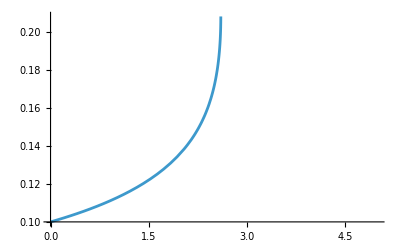

```mathematica
Plot[(a+k)/3+(2^(1/3) (3-(a+k)^2))/(3 (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))-((9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))/(3 2^(1/3))/.k->0.1,{a,0,5}]
```

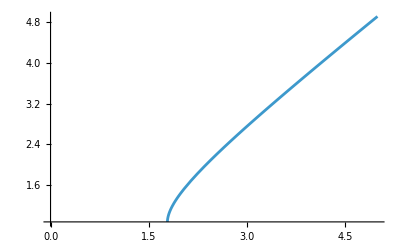

```mathematica
Plot[(a+k)/3-((1+ⅈ √3) (3-(a+k)^2))/(3 2^(2/3) (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))+((1-ⅈ √3) (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))/(6 2^(1/3))/.k->0.1,{a,0,5}]
```

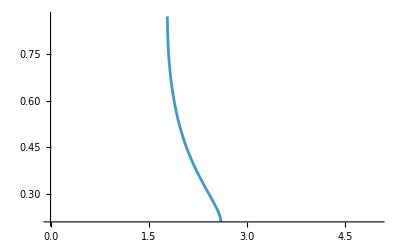

```mathematica
Plot[(a+k)/3-((1-ⅈ √3) (3-(a+k)^2))/(3 2^(2/3) (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))+((1+ⅈ √3) (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))/(6 2^(1/3))/.k->0.1,{a,0,5}]
```

```mathematica
(* All three together *)
```

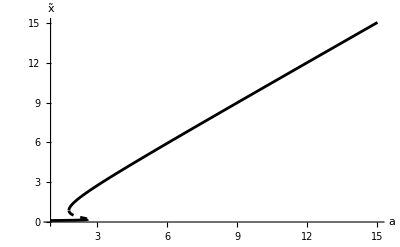

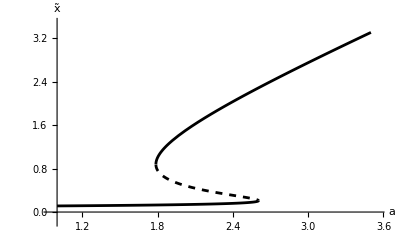

```mathematica
Plot[{(a+k)/3+(2^(1/3) (3-(a+k)^2))/(3 (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))-((9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))/(3 2^(1/3))/.k->0.1, (a+k)/3-((1-ⅈ √3) (3-(a+k)^2))/(3 2^(2/3) (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))+((1+ⅈ √3) (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))/(6 2^(1/3))/.k->0.1, (a+k)/3-((1+ⅈ √3) (3-(a+k)^2))/(3 2^(2/3) (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))+((1-ⅈ √3) (9 a-2 a^3-18 k-6 a^2 k-6 a k^2-2 k^3+3 √3 √(4-a^2-20 a k+4 a^3 k+8 k^2+12 a^2 k^2+12 a k^3+4 k^4))^(1/3))/(6 2^(1/3))/.k->0.1},{a,1,15},AxesLabel->{Style["a",16],Style[ "x̃",16]},PlotStyle->{Black,{Black, Dashed},Black}]
```

#### Trying out Sturm’s theorem

```mathematica
(*To count the number of real roots of a polynomial,see https: //math.stackexchange.com/questions/3213397/counting-the-number-of-real-roots-of-a-polynomial and https: //en.wikipedia.org/wiki/Sturm %27 s_theorem*)
(*Compare with Descartes' rule of signs: https://en.wikipedia.org/wiki/Descartes%27_rule_of_signs*)
```

Testing out the example from the website

```mathematica
-PolynomialMod[x^3+2*x+1,3x^2+2]
```

-1-(4 x)/3

```mathematica
-PolynomialMod[3x^2+2,-1-(4 x)/3]
```

-59/16

For n=2

```mathematica
-PolynomialMod[-x^3+(x^2)*(r+a)-x+r,-3*x^2+2*x*(r+a)-1]
```

-r+x/2-x^3/2

```mathematica
-PolynomialMod[-3*x^2+2*x*(r+a)-1,-r+x/2-x^3/2]
```

1-2 a x-2 r x+3 x^2

```mathematica
-PolynomialMod[-r+x/2-x^3/2,1-2 a x-2 r x+3 x^2]
```

r-x/2+x^3/2

```mathematica
-PolynomialMod[1-2 a x-2 r x+3 x^2,r-x/2+x^3/2]
```

-1+2 a x+2 r x-3 x^2

For n=3

```mathematica
D[(1+x^n)*r+a*x^n-x*(1+x^n),x]
```

-1+a n x^(-1+n)+n r x^(-1+n)-x^n-n x^n

```mathematica
-PolynomialMod[(1+x^3)*r+a*x^3-x*(1+x^3),-1+a *3* x^(-1+3)+3*r* x^(-1+3)-x^3-3* x^3]
```

-r+(2 x)/3-x^4/3

```mathematica
-PolynomialMod[-1+a *3* x^(-1+3)+3*r* x^(-1+3)-x^3-3* x^3,-r+(2 x)/3-x^4/3]
```

1-3 a x^2-3 r x^2+4 x^3

```mathematica
-PolynomialMod[-r+(2 x)/3-x^4/3,1-3 a x^2-3 r x^2+4 x^3]
```

r-(2 x)/3+x^4/3

```mathematica
-PolynomialMod[1-3 a x^2-3 r x^2+4 x^3,r-(2 x)/3+x^4/3]
```

-1+3 a x^2+3 r x^2-4 x^3

For n=8

```mathematica
-PolynomialMod[(1+x^8)*r+a*x^8-x*(1+x^8),-1+a *8* x^(-1+8)+8*r* x^(-1+8)-x^8-8* x^8]
```

-r+(7 x)/8-x^9/8

```mathematica
-PolynomialMod[-1+a *8* x^(-1+8)+8*r* x^(-1+8)-x^8-8* x^8,-r+(7 x)/8-x^9/8]
```

1-8 a x^7-8 r x^7+9 x^8

```mathematica
-PolynomialMod[-r+(7 x)/8-x^9/8,1-8 a x^7-8 r x^7+9 x^8]
```

r-(7 x)/8+x^9/8

#### Manipulate the f(x) plot, depending on a and n

```mathematica
Manipulate[{Plot[k+a*(x^n)/(1+x^n)-x/.{k->0.1,n->7},{x,0,5}]},{a,0,5}]
```